### 2018/05/14 data (ventiles)

```mathematica
ventileData[ventile_]:=Module[{data,fName,dateStr,inDir,MLTString,keeps},
inDir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/txtOutput/";
dateStr="20180514-";
MLTString="20_50-1_50MLT-";
fName=dateStr<>MLTString<>"goverkVentiles"<>ToString[ventile]<>"-allALT-NORTH-GoverK0_0-Kchi2Max0_0-allObs-normed.csv";
data=Import[inDir<>fName];
keeps=Position[data[[;;,2]],val_ /; val>0.1]//Flatten;
data=data[[keeps,;;]]
]
```

### 2018/05/16 data (21-24 MLT), ventiles

```mathematica
ventileData[ventile_]:=Module[{data,fName,dateStr,inDir,MLTString,keeps},
inDir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/txtOutput/";
dateStr="20180516-";
MLTString="21-24MLT-";
fName=dateStr<>MLTString<>"goverkVentiles"<>ToString[ventile]<>"-allALT-BOTH-GoverK0_0-Kchi2Max0_0-allObs-normed.csv";
data=Import[inDir<>fName];
keeps=Position[data[[;;,2]],val_ /; val>0.1]//Flatten; (*The purpose is to junk GoverK values less than 1 (when Maxwellian wins kappa)*)
data=data[[keeps,;;]]
]
```

Define the fit function

```mathematica
Options[fitPackage]={fitAboveKappa->2.5,fitBelowKappa->Null,Quiet->False,PrintVals->False,IncludePlot->False,ventileVal->0};
```

```mathematica
fitPackage[data_,fitFunc_,fitParms_,parmConstr_:Null,OptionsPattern[]]:=
Module[{parmVals,fitDat,lowInd,highInd,twoPlots},

(*Cut off data at low end*)
lowInd=(Position[data[[;;,1]],Min[Select[data[[;;,1]],#≥ OptionValue[fitAboveKappa]&]]]//Flatten)[[1]];
fitDat=data[[lowInd;;,;;]];

(*Cut off data at high end?*)
If[OptionValue[fitBelowKappa]≠Null,
highInd=(Position[fitDat[[;;,1]],Min[Select[fitDat[[;;,1]],#≥ OptionValue[fitBelowKappa]&]]]//Flatten)[[1]];
fitDat=fitDat[[highInd;;,;;]];
];

If[!OptionValue[Quiet],
Print[StringForm["Function: `1`",fitFunc]];
Print[StringForm["Constraints: `1`",ToString@parmConstr]];
];

(*Print[ToString[Head[parmConstr]]];*)
If[(ToString[Head[parmConstr]]==ToString[List]),
parmVals = FindFit[fitDat,{fitFunc,Evaluate[parmConstr]},fitParms,x];,
parmVals = FindFit[fitDat,fitFunc,fitParms,x];
];

If[OptionValue[PrintVals],
Print[ToString[StringForm["`1`: BEGIN",OptionValue[ventileVal]+1]]<>"\n"<>
ToString[StringForm["a = `1`",NumberForm[a/.parmVals,6]]]<>"\n"<>
ToString[StringForm["b = `1`",NumberForm[b/.parmVals,6]]]<>"\n"<>
ToString[StringForm["c = `1`",NumberForm[c/.parmVals,6]]]<>"\n"<>
"END"];
];

If[OptionValue[IncludePlot],
twoPlots=Show[Plot[(fitFunc)/.parmVals,{x,1.6,80},PlotRange->{{1.5,30},{0.9,3.0}}],ListPlot[data]];
{parmVals,twoPlots},
parmVals
]
]
```

```mathematica
fitFunc=(a x +b)^c+1;
fitParms={a,b,c};
parmConstr={-10<=c<-1,a>0};
```

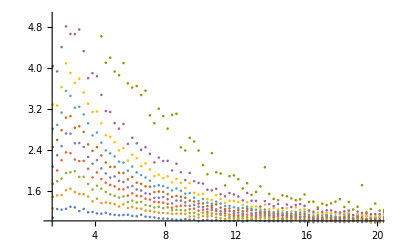

```mathematica
ListPlot[ventileData[#]&/@Range[0,18,2],PlotRange->{{1.5,20},{1,5}}]
```

```mathematica
parmVals=Table[fitPackage[ventileData[ventile],fitFunc,fitParms,parmConstr,fitBelowKappa->2.5,
ventileVal->ventile,
Quiet->True,
PrintVals->True],{ventile,0,18}];
```

1: BEGIN
a = 0.0334447
b = 1.04539
c = -9.99867
END

2: BEGIN
a = 0.029146
b = 1.00093
c = -9.9985
END

3: BEGIN
a = 0.0269885
b = 0.97667
c = -9.99832
END

4: BEGIN
a = 0.0316262
b = 0.941654
c = -8.60101
END

5: BEGIN
a = 0.0458027
b = 0.878589
c = -6.14583
END

6: BEGIN
a = 0.0474339
b = 0.848623
c = -5.77919
END

7: BEGIN
a = 0.0517204
b = 0.808367
c = -5.23105
END

8: BEGIN
a = 0.0528872
b = 0.779176
c = -5.0265
END

9: BEGIN
a = 0.0601602
b = 0.725941
c = -4.38161
END

10: BEGIN
a = 0.0568545
b = 0.717471
c = -4.45583
END

11: BEGIN
a = 0.0554643
b = 0.703853
c = -4.4301
END

12: BEGIN
a = 0.0561316
b = 0.678844
c = -4.24923
END

13: BEGIN
a = 0.0541199
b = 0.666693
c = -4.28867
END

14: BEGIN
a = 0.0494089
b = 0.672058
c = -4.52092
END

15: BEGIN
a = 0.047564
b = 0.659342
c = -4.51364
END

16: BEGIN
a = 0.049199
b = 0.620485
c = -4.22022
END

17: BEGIN
a = 0.0475008
b = 0.60024
c = -4.24058
END

18: BEGIN
a = 0.044422
b = 0.581788
c = -4.20468
END

19: BEGIN
a = 0.0674521
b = 0.161434
c = -1.62617
END

```mathematica
parmVals[[1]]
```

{a→0.0321162,b→1.05356,c→-9.99884}

```mathematica
Values@parmVals[[ventile]]
```

{0.0259515,0.954985,-9.99822}

a = 0.02595, b = 0.955, c = -9.998

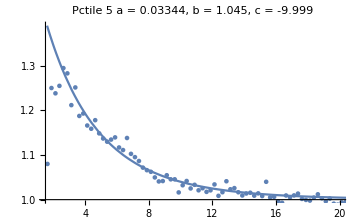
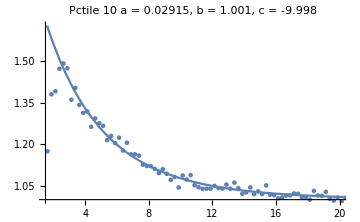
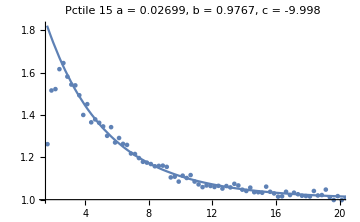
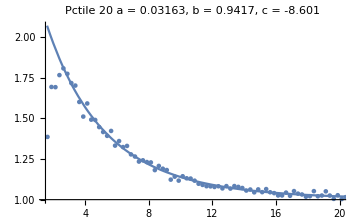
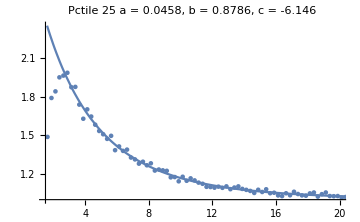
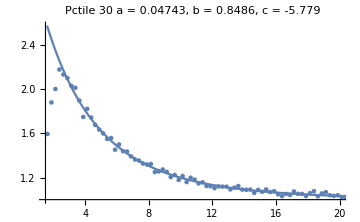
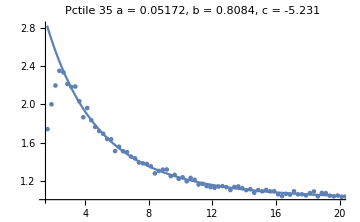
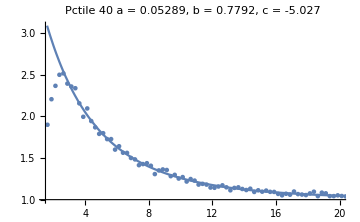

```mathematica
Table[Show[Plot[(fitFunc)/.parmVals[[ventile+1]],{x,1.6,80},PlotRange->{{1.5,20},Full},ImageSize->Medium,PlotLabel->TableForm[{{"Pctile "<>ToString[(ventile+1)*5]},
{StringForm["a = `1`, b = `2`, c = `3`",#1,#2,#3]&@@(NumberForm[#,4]&/@Values@parmVals[[ventile+1]])}}]],ListPlot[ventileData[ventile]]],{ventile,0,18}]
```